# Ejercicio 1 (P 2.24)

## Datos

```mathematica
d3=1.2;
d3p=1.2;
d5 = 3.7;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[y2, θ3,x4,θ5,x6]
Clear[vy2,ω3,vx4,ω5,vx6]
Clear[ay2,α3,ax4,α5,ax6]
```

### Ecuaciones de Posición

```mathematica
u3={Cos[θ3],Sin[θ3],0};
u5={Cos[θ5],Sin[θ5],0};
u6={Cos[Pi/4],Sin[Pi/4],0};

(*Definiendo vectores*)
R1= {2.4,0,0};
R2={0,y2,0};
R3=d3*u3;
R3p=d3p*u3;
R4={x4,0,0};
R5=d5*u5;
R6=x6*u6;

(*Lazos vectoriales*)
pos1=R4+R3+R3p-R2;
pos2=R1+R6-R5+R3p-R2;
```

### Ecuaciones de velocidad

```mathematica
(*vectores velocidades angulares*)
omega3={0,0,ω3};
omega5={0,0,ω5};

(*Definiendo vectores*)
(*V1 es vector nulo*)
V2={0,vy2,0};
V3=omega3×R3;
V3p=omega3×R3p;
V4={vx4,0,0};
V5=omega5×R5;
V6=vx6*u6;

(*Lazos vectoriales*)
vel1=V4+V3+V3p-V2;
vel2=V1+V6-V5+V3p-V2;
```

### Ecuaciones de aceleración

```mathematica
alfa3={0,0,α3};
alfa5={0,0,α5};

(*A1 es vector nulo*)
A2={0,ay2,0};
A3=alfa3×R3-ω3^2*R3;
A3p=alfa3×R3p-ω3^2*R3p;
A4={ax4,0,0};
A5=alfa5×R5-ω5^2*R5;
A6=ax6*u6;

(*Lazos vectoriales *)
acel1=A4+A3+A3p-A2;
acel2=A1+A6-A5+A3p-A2;
```

## Solución de Posición

### Solución Inicial

```mathematica
Clear[y2, θ3,x4,θ5,x6]
Clear[vy2,ω3,vx4,ω5,vx6]
Clear[ay2,α3,ax4,α5,ax6]
```

```mathematica
y2=2.05;

SolInicial = FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{θ3,115*Degree},
{x4,1.2},
{θ5,12*Degree},
{x6,2.5}},MaxIterations->15]
```

{θ3→2.11765,x4→1.248,θ5→0.220536,x6→2.59421}

```mathematica
(θ3/.SolInicial)/Degree
(θ5/.SolInicial)/Degree
```

121.332

12.6358

### Solución Total

```mathematica
Clear[y2, θ3,x4,θ5,x6]
Clear[vy2,ω3,vx4,ω5,vx6]
Clear[ay2,α3,ax4,α5,ax6]
```

```mathematica
θ3i=θ3/.SolInicial;
x4i=x4/.SolInicial;
θ5i=θ5/.SolInicial;
x6i=x6/.SolInicial;

(*Ciclo de 2.05 a 2.4*)
For[i = 205,i≥0, i-=1,
y2 = i/100;
SolPosMenor[i]= FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{θ3, θ3i},
{x4,x4i},
{θ5,θ5i},
{x6, x6i}},MaxIterations->15];
θ3i=θ3/.SolPosMenor[i];
x4i=x4/.SolPosMenor[i];
θ5i=θ5/.SolPosMenor[i];
x6i=x6/.SolPosMenor[i];]

θ3i=θ3/.SolInicial;
x4i=x4/.SolInicial;
θ5i=θ5/.SolInicial;
x6i=x6/.SolInicial;

(*Ciclo de 2.05 a 2.4*)
For[i = 205,i≤240, i+=1,
y2 = i/100;
SolPosMayor[i]= FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{θ3, θ3i},
{x4,x4i},
{θ5,θ5i},
{x6, x6i}},MaxIterations->15];
θ3i=θ3/.SolPosMayor[i];
x4i=x4/.SolPosMayor[i];
θ5i=θ5/.SolPosMayor[i];
x6i=x6/.SolPosMayor[i];]

(*Rellenando PosSol*)
For[i=0,i≤205, i+=1,
SolPos[i]=SolPosMenor[i];];
For[i=205,i≤240,i+=1,
SolPos[i]=SolPosMayor[i];];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 15 iterations.

## Gráficas de Posición

```mathematica
tabla1 = Table[{i/100,(θ3/.SolPos[i])/Degree},{i,0,240,1}];
tabla2 = Table[{i/100,x4/.SolPos[i]},{i,0,239,1}];
tabla3 = Table[{i/100,(θ5/.SolPos[i])/Degree},{i,0,240,1}];
tabla4 = Table[{i/100,x6/.SolPos[i]},{i,0,240,1}];
```

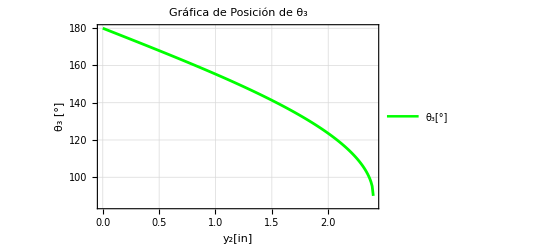

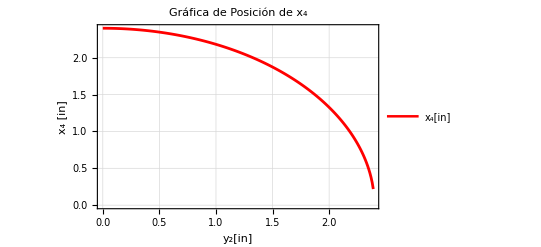

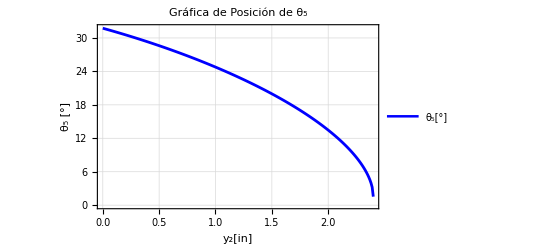

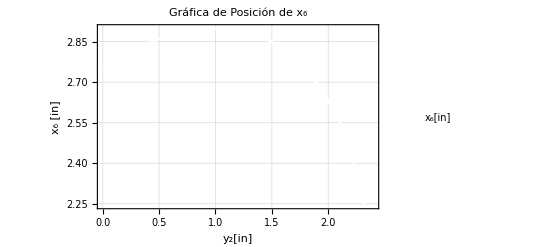

```mathematica
ListPlot[tabla1,
Frame->True,
FrameLabel->{"y_2[in]","θ_3 [°]"},
PlotLabel->"Gráfica de Posición de θ_3",
PlotLegends->{"θ_3[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla2,
Frame->True,
FrameLabel->{"y_2[in]","x_4 [in]"},
PlotLabel->"Gráfica de Posición de x_4",
PlotLegends->{"x_4[in]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla3,
Frame->True,
FrameLabel->{"y_2[in]","θ_5 [°]"},
PlotLabel->"Gráfica de Posición de θ_5",
PlotLegends->{"θ_5[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla4,
Frame->True,
FrameLabel->{"y_2[in]","x_6 [in]"},
PlotLabel->"Gráfica de Posición de x_6",
PlotLegends->{"x_6[in]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Velocidad

```mathematica
Clear[y2, θ3,x4,θ5,x6]
Clear[vy2,ω3,vx4,ω5,vx6]
Clear[ay2,α3,ax4,α5,ax6]
```

```mathematica
vy2=-15; (*in/s*)

For[i=205,i≥0,i-=1,
y2=i/100;

SolVelMenor[i]= Solve[{
vel1⟦1⟧==0,
vel1⟦2⟧==0,
vel2⟦1⟧==0,
vel2⟦2⟧==0}/.SolPosMenor[i],
{ω3,vx4,ω5,vx6}]//Flatten;];

For[i=205,i≤240,i+=1,
y2=i/100;

SolVelMayor[i]= Solve[{
vel1⟦1⟧==0,
vel1⟦2⟧==0,
vel2⟦1⟧==0,
vel2⟦2⟧==0}/.SolPosMayor[i],
{ω3,vx4,ω5,vx6}]//Flatten;];

(*Rellenando VelSol*)
For[i=0,i≤205, i+=1,
SolVel[i]=SolVelMenor[i];];
For[i=205,i≤240,i+=1,
SolVel[i]=SolVelMayor[i];];
```

## Gráficas de Velocidad

```mathematica
tabla5=Table[{i/100,ω3/.SolVel[i]},{i,0,240,1}];
tabla6=Table[{i/100,vx4/.SolVel[i]},{i,0,240,1}];
tabla7=Table[{i/100,ω5/.SolVel[i]},{i,0,240,1}];
tabla8 = Table[{i/100,vx6/.SolVel[i]},{i,0,240,1}];
```

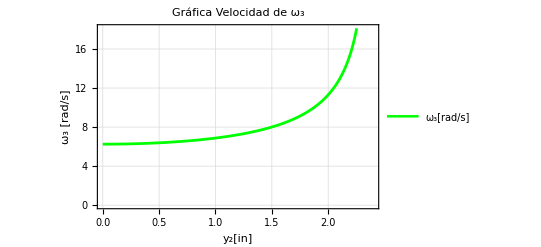

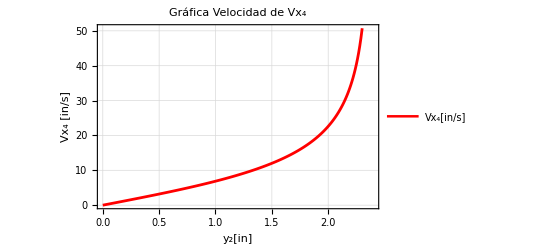

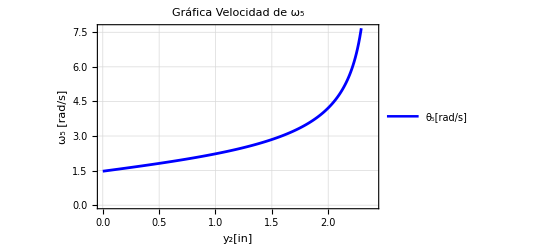

-Graphics-

```mathematica
ListPlot[tabla5,
Frame->True,
FrameLabel->{"y_2[in]","ω_3 [rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_3",
PlotLegends->{"ω_3[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla6,
Frame->True,
FrameLabel->{"y_2[in]","Vx_4 [in/s]"},
PlotLabel->"Gráfica Velocidad de Vx_4",
PlotLegends->{"Vx_4[in/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla7,
Frame->True,
FrameLabel->{"y_2[in]","ω_5 [rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_5",
PlotLegends->{"θ_5[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla8,
Frame->True,
FrameLabel->{"y_2[in]","Vx_6 [rad/s]"},
PlotLabel->"Gráfica Velocidad de Vx_6",
PlotLegends->{"Vx_6[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Aceleración

```mathematica
Clear[y2, θ3,x4,θ5,x6]
Clear[vy2,ω3,vx4,ω5,vx6]
Clear[ay2,α3,ax4,α5,ax6]
```

```mathematica
vy2=-15; (*in/s*)
ay2=6; (*in/s^2*)

For[i=205,i≥0,i-=1,
y2=i/100;

SolAcelMenor[i]= Solve[{
acel1⟦1⟧==0,
acel1⟦2⟧==0,
acel2⟦1⟧==0,
acel2⟦2⟧==0}/.SolPosMenor[i]/.SolVelMenor[i],
{α3,ax4,α5,ax6}]//Flatten;];

For[i=205,i≤240,i+=1,
y2=i/100;

SolAcelMayor[i]= Solve[{
acel1⟦1⟧==0,
acel1⟦2⟧==0,
acel2⟦1⟧==0,
acel2⟦2⟧==0}/.SolPosMayor[i]/.SolVelMayor[i],
{α3,ax4,α5,ax6}]//Flatten;];

(*Rellenando SolAcel*)
For[i=0,i≤205, i+=1,
SolAcel[i]=SolAcelMenor[i];];
For[i=205,i≤240,i+=1,
SolAcel[i]=SolAcelMayor[i];];
```

```mathematica
SolAcel[205]
```

{α3→-242.106,ax4→-676.606,α5→-89.9659,ax6→-478.128-1.41421 A1}

## Gráficas de Aceleración

```mathematica
tabla9= Table[{i/100,α3/.SolAcel[i]},{i,0,240,1}];
tabla10= Table[{i/100,ax4/.SolAcel[i]},{i,0,240,1}];
tabla11= Table[{i/100,α5/.SolAcel[i]},{i,0,240,1}];
tabla12= Table[{i,ax6/.SolAcel[i]},{i,0,240,1}];
```

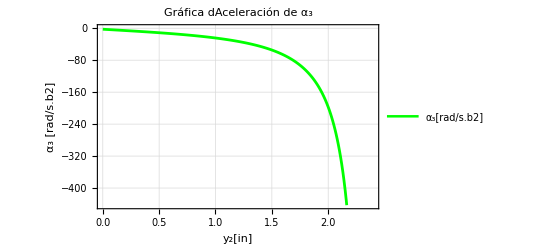

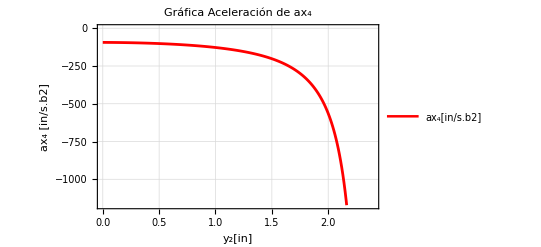

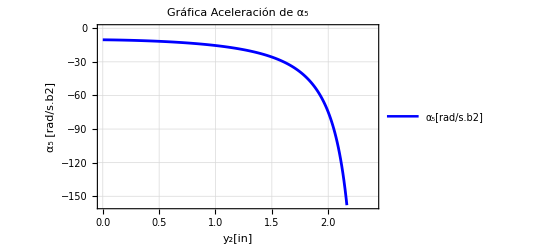

-Graphics-

```mathematica
ListPlot[tabla9,
Frame->True,
FrameLabel->{"y_2[in]","α_3 [rad/s.b2]"},
PlotLabel->"Gráfica dAceleración de α_3",
PlotLegends->{"α_3[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla10,
Frame->True,
FrameLabel->{"y_2[in]","ax_4 [in/s.b2]"},
PlotLabel->"Gráfica Aceleración de ax_4",
PlotLegends->{"ax_4[in/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla11,
Frame->True,
FrameLabel->{"y_2[in]","α_5 [rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_5",
PlotLegends->{"α_5[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla12,
Frame->True,
FrameLabel->{"y_2[in]","ax_6 [rad/s.b2]"},
PlotLabel->"Gráfica Acelerción de ax_6",
PlotLegends->{"ax_6[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Simulación

```mathematica
Clear[y2, θ3,x4,θ5,x6]

Animate[

y2=i/100;

x={1,0,0};
j={0,1,0};
k={0,0,1};
cero={0,0,0};

eslabon2=Cylinder[{R2-0.35*j,R2+0.35*j},0.3];
eslabon3=Cylinder[{R4+0.4*k,R2+0.4*k},0.1]/.SolPos[i];
eslabon4=Cylinder[{R4+0.35*x,R4-0.35*x},0.3]/.SolPos[i];
eslabon5=Cylinder[{R1+R6+0.8*k,R4+R3+0.8*k},0.1]/.SolPos[i];
eslabon6=Cylinder[{R1+R6+0.35*u6,R1+R6-0.35*u6},0.3]/.SolPos[i];

ejeA=Cylinder[{R2-0.4*k,R2+0.6*k},0.15];
ejeB=Cylinder[{R4+R3+0.1*k,R4+R3+k},0.15]/.SolPos[i];
ejeC=Cylinder[{R4-0.4*k,R4+0.6*k},0.15]/.SolPos[i];
ejeD=Cylinder[{R1+R6-0.4*k,R1+R6+k},0.15]/.SolPos[i];

(*-----CARACTERÍSTICAS-----*)

deslizador2=Graphics3D[{Orange,eslabon2}];
barra3=Graphics3D[{Green,eslabon3}];
deslizador4=Graphics3D[{Yellow,eslabon4}];
barra5=Graphics3D[{Blue,eslabon5}];
deslizador6=Graphics3D[{Purple,eslabon6}];

pernoA=Graphics3D[{Black, ejeA}];
pernoB=Graphics3D[{Black, ejeB}];
pernoC=Graphics3D[{Black, ejeC}];
pernoD=Graphics3D[{Black, ejeD}];

Show[deslizador2,barra3,deslizador4,barra5,deslizador6,pernoA,pernoB,pernoC,pernoD,
Axes->True,
AspectRatio-> Automatic,
AxesLabel-> {"X[in]","Y[in]","Z[in]"},
ImageSize-> 420,
ViewVertical-> {0,1,0},
ViewPoint-> {0,0,Infinity},
PlotRange->{{-2,5},{-2,5},{-1,5}} 
],
{i,0,240,1},
AnimationRunning->False
]
```